--- SYSTEM: Sgr A* (EHT Shadow) ---

Allowed Range: [47.2, 56.4] uas

Scanning Beta...

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

=== RESULTS (Dimensionless Units) ===

Constraint on Beta/Rs^2:

-9.038 < β/Rs^2 < 18.63

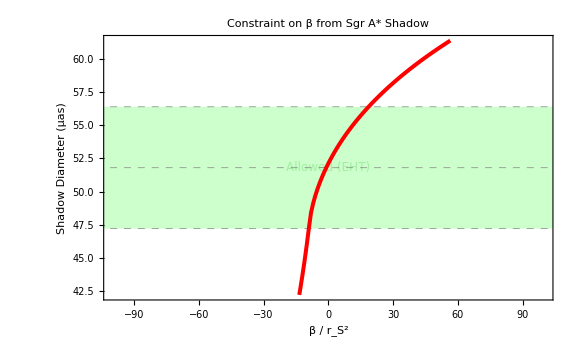

```mathematica
(*2. PHYSICAL CONSTANTS& EHT DATA*)
(* ==========================================================*)
ClearAll["Global`*"];

(*Constants (SI)*)
G=6.67430*10^-11;
c=2.99792*10^8;
Msun=1.989*10^30;
pc=3.0857*10^16;

(*Sgr A*Parameters*)
MBH=4.154*10^6*Msun;
Distance=8178*pc;
RsPhys=2*G*MBH/c^2;

(*EHT OBSERVATION*)
thetaObs=51.8;
thetaErr=2.3;
boundLower=thetaObs-2*thetaErr;
boundUpper=thetaObs+2*thetaErr;

Print["--- SYSTEM: Sgr A* (EHT Shadow) ---"];
Print["Allowed Range: [",boundLower,", ",boundUpper,"] uas"];

(* ==========================================================*)
(*3. METRIC& SHADOW SOLVER*)
(* ==========================================================*)

Afun[r_,b_]:=1.0-1.0/r-b/(48.0*r^4);

CalculateShadow[beta_?NumericQ]:=Module[{rps,Aval,bCrit,thetaRad,thetaMicro},(*Find Photon Sphere*)(*Using Quiet to suppress messages if beta creates no root*)rps=Quiet[r/. FindRoot[16*r^4-24*r^3-beta==0,{r,1.5},Method->"Newton"]];
If[!NumericQ[rps]||rps<=1.01,Return[Missing[]]];
Aval=Afun[rps,beta];
If[Aval<=0,Return[Missing[]]];
bCrit=rps/Sqrt[Aval];
thetaRad=2*(bCrit*RsPhys)/Distance;
thetaMicro=thetaRad*(180.0/Pi)*3600.0*10^6;
Return[thetaMicro];];

(* ==========================================================*)
(*4. GENERATE DATA (Using standard Table)*)
(* ==========================================================*)

scanRange=100.0;

(*Changed ParallelTable to Table to avoid LinkObject errors*)
Print["Scanning Beta..."];
data=Table[{b,CalculateShadow[b]},{b,-scanRange,scanRange,scanRange/100.0}];

data=DeleteCases[data,{_,Missing[]}];

(*Find Exact Limits*)
findBeta[target_]:=b/. FindRoot[CalculateShadow[b]-target==0,{b,0}];
limit1=findBeta[boundLower];
limit2=findBeta[boundUpper];
limits=Sort[{limit1,limit2}];

Print["\n=== RESULTS (Dimensionless Units) ==="];
Print["Constraint on Beta/Rs^2:"];
Print[NumberForm[limits[[1]],4]," < β/Rs^2 < ",NumberForm[limits[[2]],4]];

(* ==========================================================*)
(*5. PLOT*)
(* ==========================================================*)

ListLinePlot[data,Frame->True,FrameLabel->{"β / r_S^2","Shadow Diameter (μas)"},PlotStyle->{Red,Thickness[0.005]},PlotRange->{All,{boundLower-5,boundUpper+5}},GridLines->{None,{thetaObs,boundLower,boundUpper}},GridLinesStyle->Directive[Gray,Dashed],Prolog->{Directive[Green,Opacity[0.2]],Rectangle[{-1000,boundLower},{1000,boundUpper}],Text[Style["Allowed (EHT)",Darker[Green],12],{0,thetaObs}]},PlotLabel->"Constraint on β from Sgr A* Shadow",ImageSize->Large]
```